```mathematica
Table[Random[Integer],{4}]
```

{1,0,1,0}

```mathematica
NumberofHeads[m_]:=Sum[Random[Integer],{m}]
```

```mathematica
ManyTrials[m_,N_]:=Table[NumberofHeads[m],{N}]
```

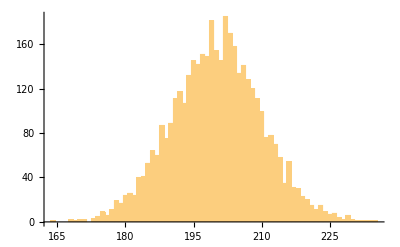

```mathematica
P1=Histogram[ManyTrials[400,4000], 60]
```

```mathematica
P2 = Plot[4000*Sqrt[2/(400*Pi)]*Exp[-2*(x-200)^2/400],{x,160,240}]
Show[P1,P2]
```